# Quantum chaos

```mathematica
Get["QMB`"]
```

## SpectralFormFactor

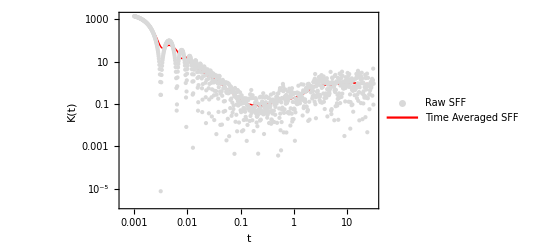

```mathematica
(* 1. Generación de un espectro GOE *)
dimension = 2000;
goeMatrix = RandomVariate[GaussianOrthogonalMatrixDistribution[dimension]];
(* Es crucial usar el espectro desplegado (Unfolded) para comparar con RMT *)
unfoldedSpectrum = Unfold[Eigenvalues[goeMatrix]]["UnfoldedLevels"];

(* 2. Definición del dominio temporal (escala logarítmica es ideal para SFF) *)
(* Heisenberg time para un espectro desplegado normalizado a 1 es t_H = 2π *)
tList = 10^Range[-3, 1.5, 0.005];

(* 3. Cálculo del SFF crudo *)
rawSFF = SpectralFormFactor[unfoldedSpectrum, tList];

(* 4. Aplicación del Promedio Temporal (Ventana de 50 puntos) *)
window = 50;
averagedSFFData = TimeAveragedSFF[tList, rawSFF, window];

(* 5. Visualización *)
ListLogLogPlot[
    {
        Transpose[{tList, rawSFF}], 
        averagedSFFData
    },
    Joined -> {False, True},
    PlotStyle -> {
        Directive[LightGray, PointSize[Small]], 
        Directive[Red, Thick]
    },
    PlotLegends -> {"Raw SFF", "Time Averaged SFF"},
    AxesLabel -> {"t", "K(t)"},
    PlotRange -> All,
    PlotTheme -> "Scientific"
]
```

## NumberVariance

```mathematica
(* 1. Generar matriz de RMT (GOE) y extraer eigenvalores *)
dim = 2000;
goeMatrix = RandomVariate[GaussianOrthogonalMatrixDistribution[dim]];
eigenvalues = Eigenvalues[goeMatrix];

(* 2. Desdoblar el espectro usando tu rutina existente Unfold[] en QMB.wl *)
unfoldData = Unfold[eigenvalues];
unfoldedLevels = unfoldData["UnfoldedLevels"];

(* 3. Parámetro de prueba: Longitud del intervalo L *)
testL = 5.0;

(* 4. Calcular Varianza Numérica vs Analítica *)
empiricalVariance = NumberVariance[unfoldedLevels, testL, 2000];
analyticalVariance = AnalyticalNumberVarianceGOE[testL];

Print["Varianza empírica \!\(\*SuperscriptBox[\(Σ\), \(2\)]\) (L=", testL, "): ", empiricalVariance];
Print["Varianza analítica GOE: ", analyticalVariance];
```

Varianza empírica Σ^2 (L=5.): 0.753946

Varianza analítica GOE: 0.768183

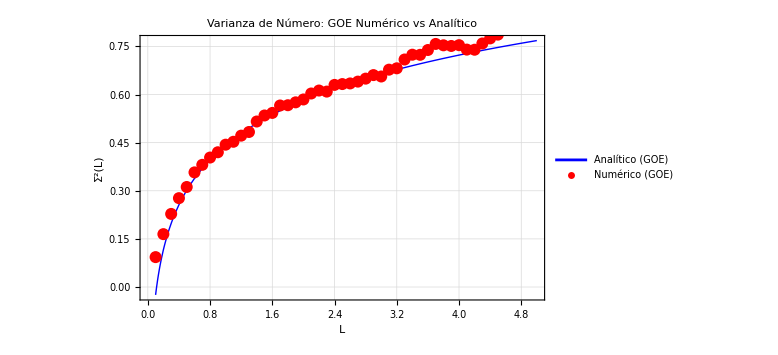

```mathematica
(* 1. Generar matriz de RMT (GOE) y extraer eigenvalores *)
DimensionMatriz = 2000;
MatrizGOE = RandomVariate[GaussianOrthogonalMatrixDistribution[DimensionMatriz]];
EigenvaloresGOE = Eigenvalues[MatrizGOE];

(* 2. Desdoblar el espectro usando tu rutina existente Unfold[] en QMB.wl *)
DatosDesdoblados = Unfold[EigenvaloresGOE];
NivelesDesdoblados = DatosDesdoblados["UnfoldedLevels"];

(* 3. Generar el rango de L (evitando L=0 exacto por la divergencia del Logaritmo) *)
RangoL = Range[0.1, 5.0, 0.1];

(* 4. Calcular la Varianza Numérica mapeando la función puramente funcional *)
VarianzaEmpirica = NumberVariance[NivelesDesdoblados, #, 2000] & /@ RangoL;
PuntosEmpiricos = Transpose[{RangoL, VarianzaEmpirica}];

(* 5. Construcción de los gráficos *)
GraficaEmpirica = ListPlot[
    PuntosEmpiricos,
    PlotStyle -> Directive[PointSize[0.015], Red],
    PlotLegends -> {"Numérico (GOE)"}
];

GraficaAnalitica = Plot[
    AnalyticalNumberVarianceGOE[l],
    {l, 0.1, 5.0},
    PlotStyle -> Directive[Thick, Blue],
    PlotLegends -> {"Analítico (GOE)"},
    AxesOrigin -> {0, 0}
];

(* 6. Renderizado final combinando numérico y analítico *)
GraficaFinal = Show[
    GraficaAnalitica,
    GraficaEmpirica,
    Frame -> True,
    FrameLabel -> {"L", "\!\(\*SuperscriptBox[\(Σ\), \(2\)]\)(L)"},
    PlotLabel -> "Varianza de Número: GOE Numérico vs Analítico",
    GridLines -> Automatic,
    ImageSize -> Large
]
```